```mathematica
ccColor=RGBColor["#ff1f5b"];
```

```mathematica
ctColor=Blue;
```

```mathematica
(***************************)
```

```mathematica
dateMouseSessionListV1CC={{"051623","Mouse23112","Session1"},{"051723","Mouse23112","Session1"},{"051623","Mouse23166","Session1"},{"051723","Mouse23166","Session1"},{"043023","Mouse23184","Session1"},{"050123","Mouse23184","Session1"},{"050423","Mouse23184","Session1"},{"052523","Mouse23158","Session1"},{"052923","Mouse23158","Session1"}};
```

```mathematica
dateMouseSessionListV1CT={{"041823","Mouse21531","Session1"},{"041923","Mouse21531","Session1"},{"041823","Mouse23138","Session1"},{"041923","Mouse23138","Session1"},{"042023","Mouse23138","Session1"},{"050523","Mouse23195","Session1"},{"051723","Mouse21532","Session1"},{"051823","Mouse21532","Session1"},{"052523","Mouse23195","Session1"}};
```

```mathematica
(**********************************************)
(*******Generate plots in Figure S4G****************) 
(**********************************************)
```

```mathematica
meanDFFzOnsetV1CC=ToExpression/@Import["F:/FigureGeneration/FigureS4/FigureS4Data/V1CC/ValuesForPlotting/meanDFFzTraceOnset_V1CC_nonDupROIs.txt","List"];
```

```mathematica
semDFFzOnsetV1CC=ToExpression/@Import["F:/FigureGeneration/FigureS4/FigureS4Data/V1CC/ValuesForPlotting/semDFFzTraceOnset_V1CC_nonDupROIs.txt","List"];
```

```mathematica
meanDFFzOffsetV1CC=ToExpression/@Import["F:/FigureGeneration/FigureS4/FigureS4Data/V1CC/ValuesForPlotting/meanDFFzTraceOffset_V1CC_nonDupROIs.txt","List"];
```

```mathematica
semDFFzOffsetV1CC=ToExpression/@Import["F:/FigureGeneration/FigureS4/FigureS4Data/V1CC/ValuesForPlotting/semDFFzTraceOffset_V1CC_nonDupROIs.txt","List"];
```

```mathematica
meanDFFzOnsetV1CT=ToExpression/@Import["F:/FigureGeneration/FigureS4/FigureS4Data/V1CT/ValuesForPlotting/meanDFFzTraceOnset_V1CT_nonDupROIs.txt","List"];
```

```mathematica
semDFFzOnsetV1CT=ToExpression/@Import["F:/FigureGeneration/FigureS4/FigureS4Data/V1CT/ValuesForPlotting/semDFFzTraceOnset_V1CT_nonDupROIs.txt","List"];
```

```mathematica
meanDFFzOffsetV1CT=ToExpression/@Import["F:/FigureGeneration/FigureS4/FigureS4Data/V1CT/ValuesForPlotting/meanDFFzTraceOffset_V1CT_nonDupROIs.txt","List"];
```

```mathematica
semDFFzOffsetV1CT=ToExpression/@Import["F:/FigureGeneration/FigureS4/FigureS4Data/V1CT/ValuesForPlotting/semDFFzTraceOffset_V1CT_nonDupROIs.txt","List"];
```

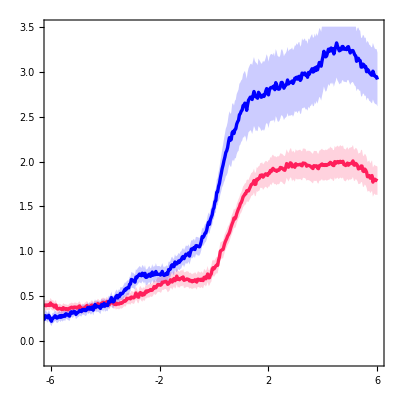

```mathematica
ListLinePlot[{Part[#,2]&/@meanDFFzOnsetV1CC,Part[#,2]&/@meanDFFzOnsetV1CC+(Part[#,2]&/@semDFFzOnsetV1CC),Part[#,2]&/@meanDFFzOnsetV1CC-(Part[#,2]&/@semDFFzOnsetV1CC),Part[#,2]&/@meanDFFzOnsetV1CT,Part[#,2]&/@meanDFFzOnsetV1CT+(Part[#,2]&/@semDFFzOnsetV1CT),Part[#,2]&/@meanDFFzOnsetV1CT-(Part[#,2]&/@semDFFzOnsetV1CT)},Filling->{1->{{2},Directive[Opacity[0.2],ccColor]},1->{{3},Directive[Opacity[0.2],ccColor]},4->{{5},Directive[Opacity[0.2],ctColor]},4->{{6},Directive[Opacity[0.2],ctColor]}},PlotStyle->{{ccColor,Thickness[0.006]},Transparent,Transparent,{ctColor,Thickness[0.006]},Transparent,Transparent},DataRange->{-15,6},PlotRange->{{-6,6},{-0.2,3.5}},FrameTicks->{{LinTicks[-0.2,3.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-6,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

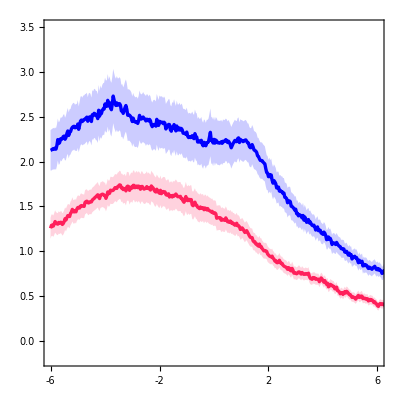

```mathematica
ListLinePlot[{Part[#,2]&/@meanDFFzOffsetV1CC,Part[#,2]&/@meanDFFzOffsetV1CC+(Part[#,2]&/@semDFFzOffsetV1CC),Part[#,2]&/@meanDFFzOffsetV1CC-(Part[#,2]&/@semDFFzOffsetV1CC),Part[#,2]&/@meanDFFzOffsetV1CT,Part[#,2]&/@meanDFFzOffsetV1CT+(Part[#,2]&/@semDFFzOffsetV1CT),Part[#,2]&/@meanDFFzOffsetV1CT-(Part[#,2]&/@semDFFzOffsetV1CT)},Filling->{1->{{2},Directive[Opacity[0.2],ccColor]},1->{{3},Directive[Opacity[0.2],ccColor]},4->{{5},Directive[Opacity[0.2],ctColor]},4->{{6},Directive[Opacity[0.2],ctColor]}},PlotStyle->{{ccColor,Thickness[0.006]},Transparent,Transparent,{ctColor,Thickness[0.006]},Transparent,Transparent},DataRange->{-6,15},PlotRange->{{-6,6},{-0.2,3.5}},FrameTicks->{{LinTicks[-0.2,3.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-6,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

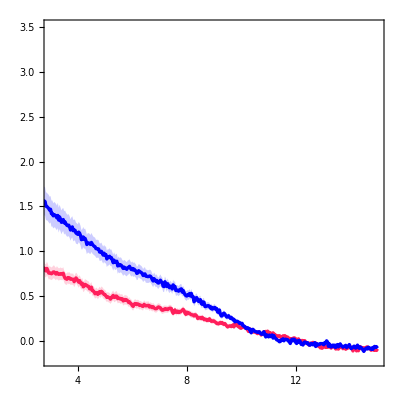

```mathematica
ListLinePlot[{Part[#,2]&/@meanDFFzOffsetV1CC,Part[#,2]&/@meanDFFzOffsetV1CC+(Part[#,2]&/@semDFFzOffsetV1CC),Part[#,2]&/@meanDFFzOffsetV1CC-(Part[#,2]&/@semDFFzOffsetV1CC),Part[#,2]&/@meanDFFzOffsetV1CT,Part[#,2]&/@meanDFFzOffsetV1CT+(Part[#,2]&/@semDFFzOffsetV1CT),Part[#,2]&/@meanDFFzOffsetV1CT-(Part[#,2]&/@semDFFzOffsetV1CT)},Filling->{1->{{2},Directive[Opacity[0.2],ccColor]},1->{{3},Directive[Opacity[0.2],ccColor]},4->{{5},Directive[Opacity[0.2],ctColor]},4->{{6},Directive[Opacity[0.2],ctColor]}},PlotStyle->{{ccColor,Thickness[0.006]},Transparent,Transparent,{ctColor,Thickness[0.006]},Transparent,Transparent},DataRange->{-6,15},PlotRange->{{3,15},{-0.2,3.5}},FrameTicks->{{LinTicks[-0.2,3.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[3,15,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
(***Import overall loc mod values***)
```

```mathematica
locModValsV1CC=ToExpression/@Import["F:/FigureGeneration/FigureS4/FigureS4Data/V1CC/ValuesForPlotting/locModIndexSummVals_V1CC_nonDupROIs.txt","List"];
```

```mathematica
locModValsV1CT=ToExpression/@Import["F:/FigureGeneration/FigureS4/FigureS4Data/V1CT/ValuesForPlotting/locModIndexSummVals_V1CT_nonDupROIs.txt","List"];
```

```mathematica
(**********************)
```

```mathematica
ccAxonCharts=Show[BoxWhiskerChart[locModValsV1CC,{{"Whiskers", Directive[Darker@ccColor,Thick]}, {"Fences", Directive[Darker@ccColor,Thick]},{"MedianMarker", Directive[Darker@ccColor,Thickness[0.009]]}},PlotRange->{All,{-1.2,1}},ChartStyle->Directive[ccColor,Opacity[0.3]],Frame->False],DistributionChart[locModValsV1CC,PlotRange->{All,{-1.2,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],ccColor],Frame->False],FrameTicks->{{LinTicks[-1.2,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
ctAxonCharts=Show[BoxWhiskerChart[locModValsV1CT,{{"Whiskers", Directive[Darker@ctColor,Thick]}, {"Fences", Directive[Darker@ctColor,Thick]},{"MedianMarker", Directive[Darker@ctColor,Thickness[0.009]]}},PlotRange->{All,{-1.2,1}},ChartStyle->Directive[ctColor,Opacity[0.3]],Frame->False],DistributionChart[locModValsV1CT,PlotRange->{All,{-1.2,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],ctColor],Frame->False],FrameTicks->{{LinTicks[-1.2,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[locModValsV1CT,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{-1.2,1}},ChartStyle->Transparent,Frame->False],DistributionChart[locModValsV1CT,PlotRange->{All,{-1.2,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[-1.2,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

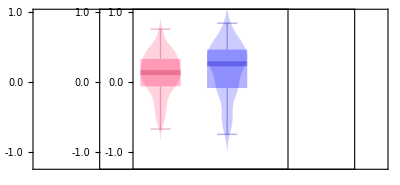

```mathematica
GraphicsRow[{ccAxonCharts,ctAxonCharts,transp},Spacings->{{-280,-280,-320}}]
```